Find any sting cell lineages (if they exist)

```mathematica
SetDirectory["D:\\newLight3"]
```

D:\newLight3

```mathematica
indexOfSting=2;
```

```mathematica
GetNumberOfSting[frameNo_]:=Module[{path,file,headings,applyHeading,items,nOrganisms,nFertile},
path = StringForm["output\\frame``.csv",frameNo];
file=Import[path//ToString];
headings=file//First;
items=file//Rest;
applyHeading[item_]:=MapThread[#1-> #2&,{headings,item}];
items = applyHeading/@items;
Cases[{"o","ct"}/.items,{o_/;o≥0,indexOfSting}->o]//DeleteDuplicates
]
```

```mathematica
GetOrganism[orgNo_]:=With[{path=StringForm["organisms\\org``.json",orgNo]//ToString},
Import[path]
]
```

```mathematica
(("parent"/.GetOrganism[#])-># )&/@Take[sting,10]
```

{2→47,7→85,227→324,227→327,33→121,64→227,47→234,68→189,178→208,85→252}

```mathematica
f0=0;
fMax=1160000;
df=10000;
frames=Table[f,{f,f0,fMax,df}];
sting=ParallelMap[GetNumberOfSting,frames]//Flatten//DeleteDuplicates;
```

```mathematica
sting//Length
```

10107

```mathematica
stingAndParents=ParallelMap[(("parent"/.GetOrganism[#])-># )&,sting];
```

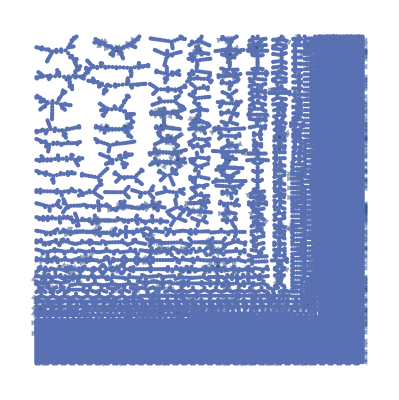

```mathematica
g=Graph[stingAndParents]
```

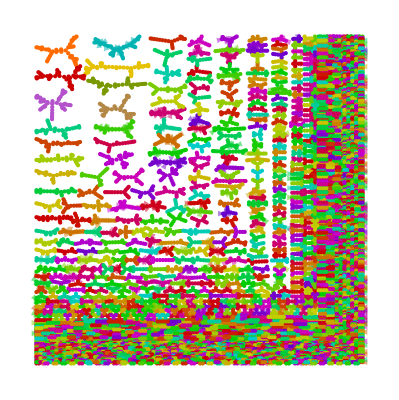

```mathematica
relatives=WeaklyConnectedComponents[g];
HighlightGraph[g,Subgraph[g,#]&/@relatives]
```

```mathematica
largestRelativeGroup=MaximalBy[relatives,Length]//Flatten
```

{630577,629146,631054,631883,628296,632306,634099,626794,628861,630759,625747,627885,627899,628514,629999,629816,630744,632326,624933,630163,632248,631602,630075,632213,634664,633736,625781,626019,633022,633545,632773,633071,630807,625923,627362,628369,628627,633241,627412,626094,628018,629101,627661,626750,627752,630605,630914,634396,632703,635013,634672,634960}

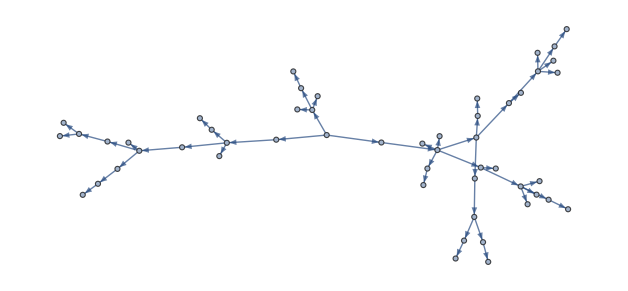

```mathematica
g2=Subgraph[Graph[ParallelMap[(("parent"/.GetOrganism[#])-># )&,largestRelativeGroup]],
largestRelativeGroup]
```

```mathematica
InfoCard2[GetOrgInfo[10]]
```

-Graphics3D-
ID | 10
Birth | 13702
Viewed | 14050
Death | 14400
Gen# | 3

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Riffle::list: List expected at position 1 in Riffle[ct,Sphere[{x,z,y},r]].

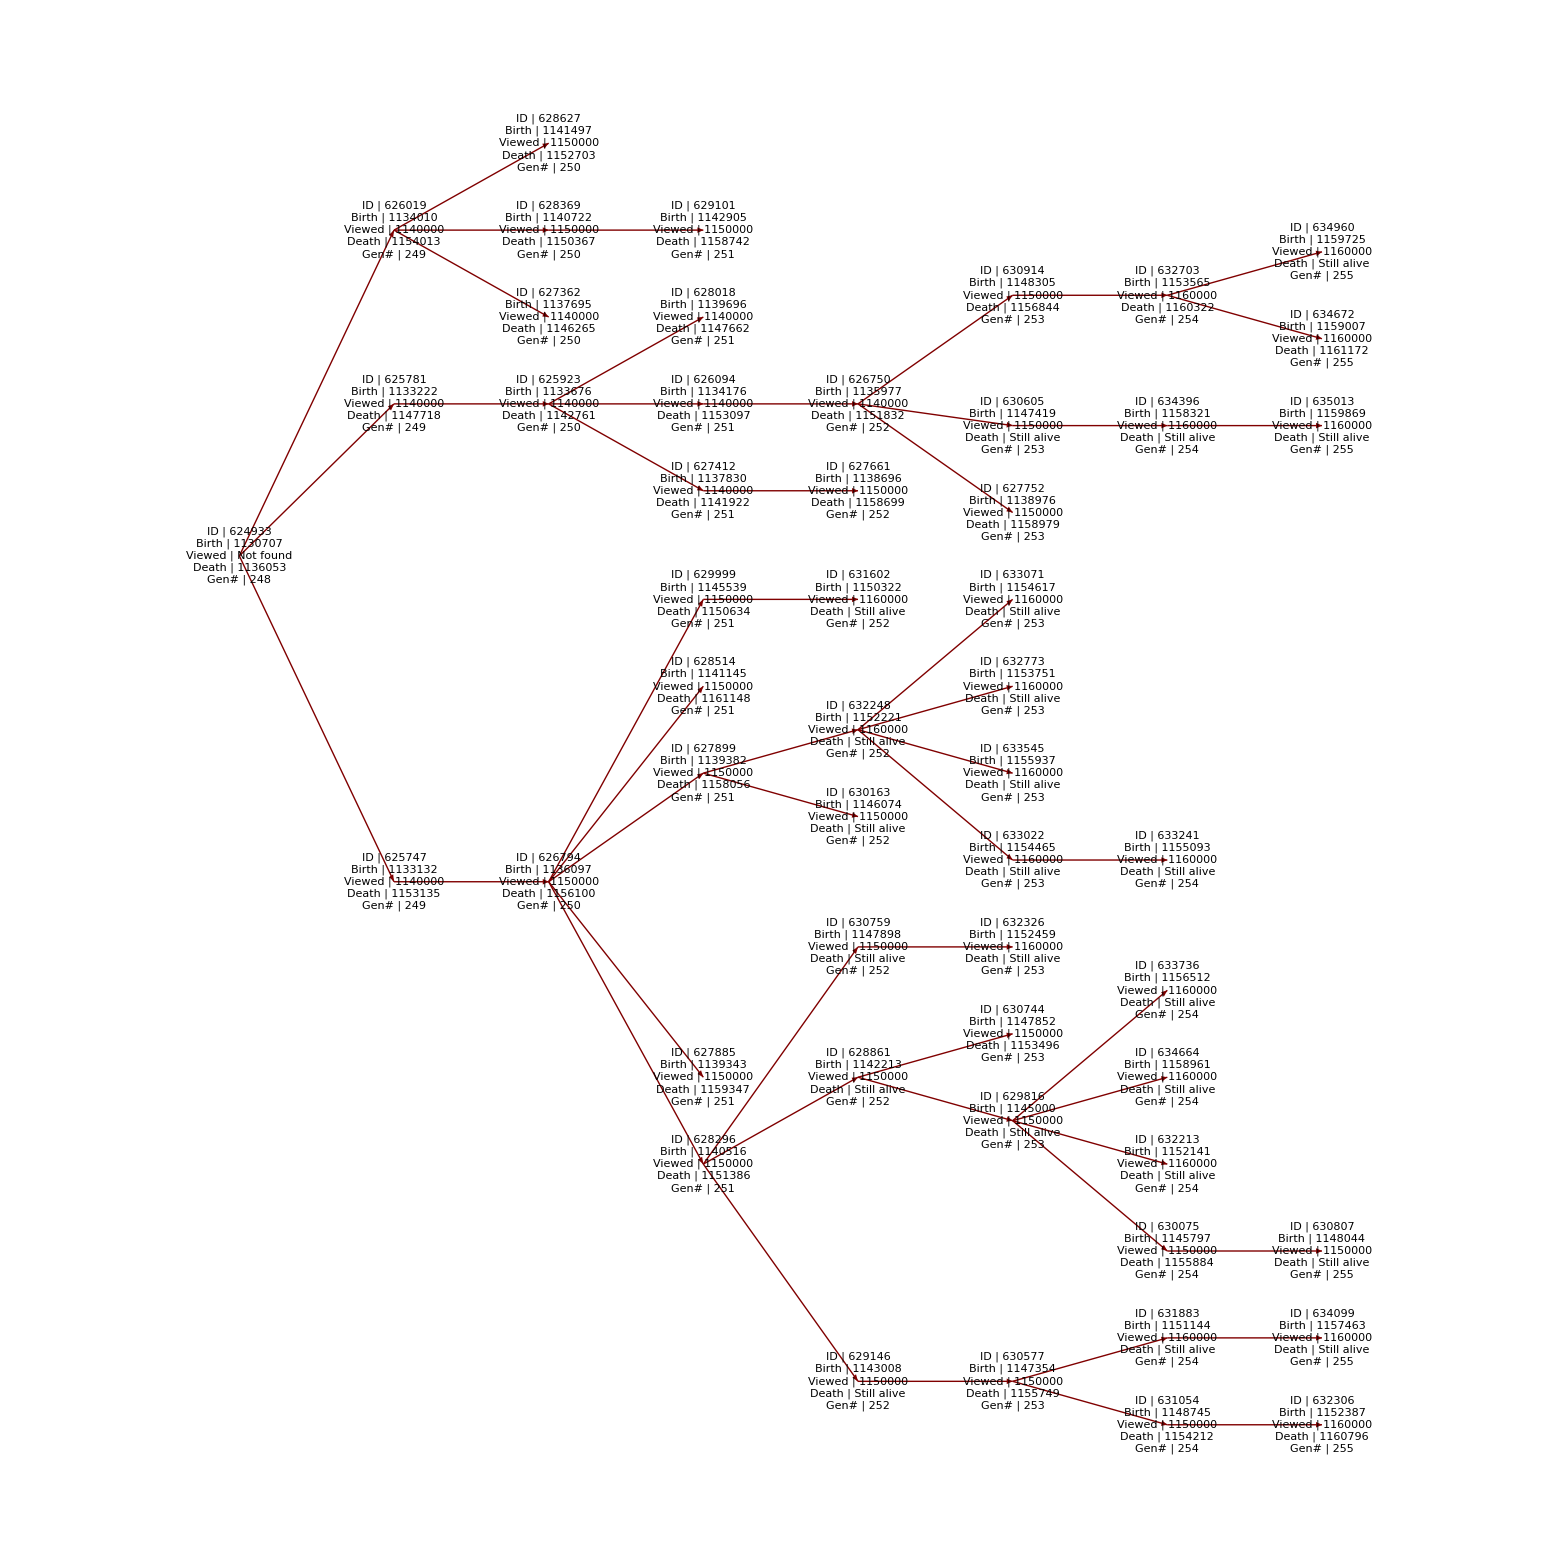

```mathematica
root=Ordering[largestRelativeGroup,1]//First;
TreePlot[g2,Left,
root,
VertexRenderingFunction-> (Inset[VisualizeOrg[GetOrgInfo[largestRelativeGroup⟦#2⟧]],#1]&),
ImageSize->Full,VertexLabeling->True
]
```

These organisms have more egg cells than the surface-living organisms. This could be due to the fact that they gain large amounts of energy at the time, thus it would be a waste to only have one egg cell.